## 136Nd - Petrache Study

## The 2-phonon structure (bands 2-5-6)

-Graphics-

According to Ref. “Evolution from y-soft to stable triaxiality in 136 Nd as a prerequisite of chirality”, the bands [2,5,6] are [L1,L3,(T1+L4)]

```mathematica
ClearAll["Global`*"]
```

```mathematica
band2En=Sort[N[#/1000]&@{8615,7349,6188,5189,4345,3684,3294}];
band5En=Sort[N[#/1000]&@{8098,6928,5940,5130,4452}];
band6En=Sort[N[#/1000]&@{9171,8222,7329,6470,5568,4853}];
band2Spins=Table[i,{i,10,22,2}];
band5Spins=Table[i,{i,13,21,2}];
band6Spins=Table[i,{i,14,24,2}];
```

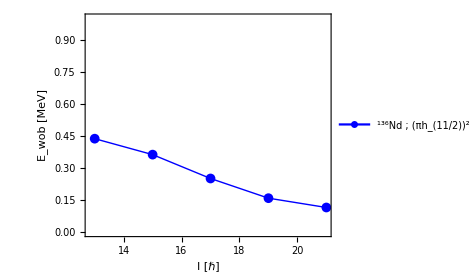

```mathematica
m1minipath="/Users/basavyr/Documents/DevWorkspace/GitHub/mathematica-useful-algorithms/Physics/experimental-data-collection-wobblers/Nd-Nuclei/136Nd-2.pdf";
wobbling[yrast_,onephonon_,onespins_]:=Table[{onespins[[i]],onephonon[[i]]-1/2(yrast[[i+1]]+yrast[[i+2]])},{i,1,Length[onephonon]}];
data=wobbling[band2En,band5En,band5Spins];
fig=ListPlot[data,Joined->True,PlotMarkers->{Automatic, Medium},Frame->True,Axes->False,AspectRatio->0.8,PlotStyle->{Thick,Blue},FrameStyle->Directive[Thick,Black],FrameLabel->{"I [ℏ]","E_wob [MeV]"},LabelStyle->{20,Bold,Black,FontFamily->"Arial"},PlotLegends->Placed[{Style[Row[{Superscript["","136"],"Nd ; (πh_(11/2))^2"}],FontFamily->"Times",30]},{0.5,0.85}],ImageSize->350,PlotRange->{Full,{0,1}}];
Export[m1minipath,fig];
Show[fig]
```